# Rollups benchmarks

## Benchmarking exec units as a function of “update length”

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Reference protocol parameters (June 2023)

```mathematica
maxExSteps=10000000000;
maxExMem=14000000;
```

#### Import benchmark data

```mathematica
data=Import["rollupBench_1.csv","CSV"];
```

## Data analysis

### CPU

```mathematica
cpuData={#⟦1⟧,#⟦2⟧}&/@data
```

{{0,4128437479},{50,4480400069},{100,4832362659},{150,5181116939},{200,5533079529},{250,5885042119},{300,6237004709},{350,6585758989},{400,6937721579},{450,7289684169},{500,7641646759},{550,7990401039},{600,8342363629},{650,8694326219},{700,9046288809},{750,9395043089},{800,9747005679},{850,10098968269},{900,10450930859},{950,10799685139},{1000,11151647729}}

#### Data plot (CPU)

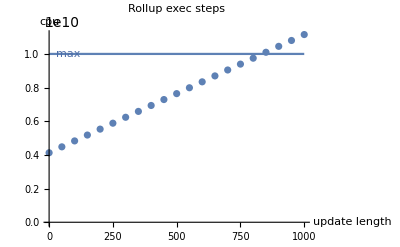

```mathematica
ListPlot[cpuData,PlotRange->All,
PlotLabel->"Rollup exec steps",AxesLabel->{"update length","cpu"}];
Plot[maxExSteps,{x,0,First@Last[cpuData]}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{75,maxExSteps},{0,-1}]];
cpuPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[cpuData][ul]==maxExSteps,{ul,40}]
```

{ul→835.941}

∴ CPU budget is exceded when update length is ≥ 836 .

### Memory

```mathematica
memData={#⟦1⟧,#⟦3⟧}&/@data
```

{{0,2047436},{50,2965536},{100,3883636},{150,4781736},{200,5699836},{250,6617936},{300,7536036},{350,8434136},{400,9352236},{450,10270336},{500,11188436},{550,12086536},{600,13004636},{650,13922736},{700,14840836},{750,15738936},{800,16657036},{850,17575136},{900,18493236},{950,19391336},{1000,20309436}}

#### Data plot (memory)

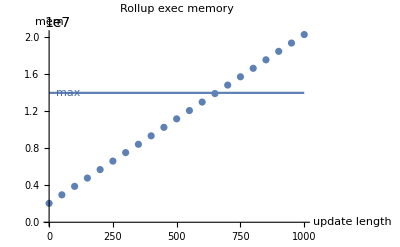

```mathematica
ListPlot[memData,PlotRange->All,
PlotLabel->"Rollup exec memory",AxesLabel->{"update length","mem"}];
Plot[maxExMem,{x,0,First@Last[cpuData]}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{75,maxExMem},{0,-1}]];
memPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[memData][ul]==maxExMem,{ul,40}]
```

{ul→654.193}

∴ Memory budget is exceded when update length is ≥ 655 .

## Conclusion

To be within exec units budget, update length must be 654 or less.

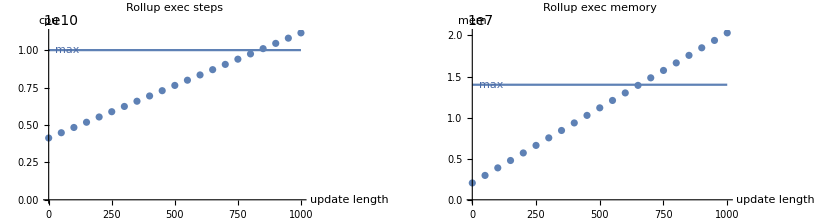

```mathematica
GraphicsRow[{cpuPlot,memPlot}]
```